## Depict Tiles

### General Tile

```mathematica
TileVertices[step_][or_,dir_,ref_,pt_] := With[{
basicVertices = AnglePath[{
		{step[[2]], -Pi/6+dir*Pi/6},
		{step[[2]], Pi/3},
		{step[[1]], Pi/2},
		{step[[1]], Pi/3},
		{step[[2]], -Pi/2},
		{step[[2]], Pi/3},
		{step[[1]], Pi/2},
		{step[[1]], -Pi/3},
		{step[[2]], Pi/2},
		{step[[2]], -Pi/3},
		{step[[1]], Pi/2},
		{step[[1]], Pi/3},
		{step[[1]], 0}
	}]
},
	Expand[(If[ref,{-#[[1]], #[[2]]}, #] & /@ ( basicVertices - Threaded[basicVertices[[pt]]] ) ) + Threaded[or]]
]
```

```mathematica
TileEdges[step_][or_,dir_,ref_,pt_] := Partition[TileVertices[step][or,dir,ref,pt], 2, 1, 1]
```

```mathematica
Tile[step_][or_,dir_,ref_,pt_] := Polygon[TileVertices[step][or,dir,ref,pt]]
```

### Hat, Turtle, Spectre

```mathematica
hatVertices:=TileVertices[{1, Sqrt[3]}];
hatEdges:=TileEdges[{1, Sqrt[3]}];
hat:=Tile[{1, Sqrt[3]}];
```

```mathematica
turtleVertices := TileVertices[{Sqrt[3], 1}];
turtleEdges := TileEdges[{Sqrt[3],1}];
turtle := Tile[{Sqrt[3], 1}];
```

```mathematica
spectreVertices := TileVertices[{1, 1}];
spectreEdges := TileEdges[{1,1}];
spectre := Tile[{1, 1}];
```

## Main Idea

Build a topological graph to describe how tiles connect with each other.

The key is what information Vertex and Edge in graph should record.

Vertex must record vertex configuration, 1/3 v.f. Edge should record the relative position between two vertices in graph.

A vertex/point in tiling can be a Vertex in graph, and a tile is an Edge in graph, indicating how these vertices connect to each other.

Aim: build a topological graph from given hat tiling, then, we build combinatorial equivalent tiling with this graph, using other tiles, like H8.

## Preparation, Generalizing Hat 1/3 V.F

```mathematica
color={{4,4,5}->Hue[Rational[1, 9]],{2,4,5}->Hue[Rational[2, 9]],{2,4,4}->Hue[Rational[1, 3]],{2,2,4}->Hue[Rational[4, 9]],{2,2,2}->Hue[Rational[5, 9]],{1,3,3}->Hue[Rational[2, 3]],{1,1,3}->Hue[Rational[7, 9]],{1,1,1}->Hue[Rational[8, 9]]};
```

```mathematica
hatVerticesToControlPoints={2->1,4->2,6->3,12->4,14->5};
```

```mathematica
canonicalVertexConfiguration=Apply[{#1,#2,#3/.hatVerticesToControlPoints}&,oneThirdVertexTheoremLis[{1,Sqrt[3]}],{2}]
```

{{{0,False,4},{8,False,4},{2,False,5}},{{0,False,2},{2,False,4},{8,False,5}},{{0,False,2},{2,False,4},{10,False,4}},{{0,False,2},{4,False,2},{2,False,4}},{{0,False,2},{4,False,2},{8,False,2}},{{0,False,1},{0,False,3},{4,False,3}},{{0,False,1},{4,False,1},{4,False,3}},{{0,False,1},{4,False,1},{8,False,1}}}

```mathematica
codeAllRotations=Function[dir,Apply[{Mod[#1+dir,12],#2,#3}&,#,{1}]]/@Range[0,11]&;
```

```mathematica
codeAllRotations[canonicalVertexConfiguration[[1]]]//Column
```

{{0,False,4},{8,False,4},{2,False,5}}
{{1,False,4},{9,False,4},{3,False,5}}
{{2,False,4},{10,False,4},{4,False,5}}
{{3,False,4},{11,False,4},{5,False,5}}
{{4,False,4},{0,False,4},{6,False,5}}
{{5,False,4},{1,False,4},{7,False,5}}
{{6,False,4},{2,False,4},{8,False,5}}
{{7,False,4},{3,False,4},{9,False,5}}
{{8,False,4},{4,False,4},{10,False,5}}
{{9,False,4},{5,False,4},{11,False,5}}
{{10,False,4},{6,False,4},{0,False,5}}
{{11,False,4},{7,False,4},{1,False,5}}

```mathematica
$vertexConfigurations=codeAllRotations/@canonicalVertexConfiguration;
```

```mathematica
$vertexConfigurations//Iconize
```

```mathematica
$vertexConfigurations=;
```

## Tile Data Structure

### format data structure association

```mathematica
formatTile[polygon_Polygon,vertices_List]:=<|"polygonVertices"->First[polygon],"vertices"->vertices|>;
```

```mathematica
formatTile[polygonVertices_List,vertices_List]:=<|"polygonVertices"->polygonVertices,"vertices"->vertices|>;
```

### put tile at a certain location

```mathematica
locateTile[tile_Association][pos_List,dir_Integer,pt_Integer]:=With[{
transformFunction=TranslationTransform[pos]@*RotationTransform[dir*Pi/6]@*TranslationTransform[-tile["vertices"][[pt]]]
},
transformFunction/@tile
]
```

### some tiles information

```mathematica
h1Tile=;
h2Tile=;
h8Tile=;
h7Tile=;
```

### visualization

```mathematica
depictTile[tile_Association,PointShow_:True,color_:Lighter@Blue,pointsize_:.3]:=Graphics[{
Opacity[.5],EdgeForm[Black],color,Polygon[tile["polygonVertices"]],
If[TrueQ[PointShow],Sequence@@{
ColorNegate[color],
Disk[tile["vertices"],pointsize]
},Nothing]
}]
```

```mathematica
depictTile/@{h1Tile,h2Tile,h8Tile,h7Tile}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Vertex configuration

```mathematica
Partition[
Row[{##},Style["→",40]]&@@@Transpose[
Function[tile,
Show[depictTile/@(locateTile[tile][{0,0},#1,#3]&@@@$vertexConfigurations[[#,1]]),ImageSize->130]&/@Range[8]
]/@{h1Tile,h8Tile,h8supertile}
],2]//Grid[#,Frame->All,FrameStyle->LightGray]&
```

-Graphics-→-Graphics-→-Graphics- | -Graphics-→-Graphics-→-Graphics-
-Graphics-→-Graphics-→-Graphics- | -Graphics-→-Graphics-→-Graphics-
-Graphics-→-Graphics-→-Graphics- | -Graphics-→-Graphics-→-Graphics-
-Graphics-→-Graphics-→-Graphics- | -Graphics-→-Graphics-→-Graphics-

## 2 Test data

Some traditional data.

```mathematica
testdata1=;(*super-tile data*)
testdata2=;(*{6,6,6} dead end data*)
```

These are hat tile codes from grow function, which represent reflected and unreflected tiles respectively. We need to merge reflected tiles with one hat tile to make H2.

Traditional hat tile code represent reflected tile and unreflected tile respectively, as each individual. But combinatorial equivalence requires us to merge reflected tile with one neighbor tile to be H2. This is done by the following function.

This function preprocesses traditional hat tile code {pos, dir, parity, pt} into {pos, dir, pt, parity} where parity indicate whether its tile1, or tile 2. (H1 or H2, H7 or H8 and so on). pt has range 1~5, indicating 1/3 key vertices of tiles.

```mathematica
codePreprocess=Function[codes,
With[{refs=Cases[codes,reftile_?(MemberQ[True]):>First[hatVertices@@reftile]]},
{
(hatVertices[#[[1]],#[[2]],False,#[[4]]])[[2]],
#[[2]],1,#[[3]]
}&/@
Replace[
DeleteCases[codes,_?(MemberQ[True])],
tile_/;MemberQ[refs,(hatVertices@@tile)[[9]]]:>({tile[[1]],tile[[2]],True,tile[[4]]}),
{1}
]
]
];
```

This is process result, H2 is merged, and each tile is represented by its 1/3 vertices.

```mathematica
Show[
depictTile[
locateTile[If[TrueQ[#4],h2Tile,h1Tile]][#1,#2,#3],
True,
If[TrueQ[#4],ColorNegate[Blue],Lighter@Blue]
]&@@@codePreprocess[#]
]&/@{testdata1,testdata2}//GraphicsRow
```

-Graphics-

## Build Topological Graph from Hat tiling

### Tiling topological graph constructor

```mathematica
tilingTopologicalGraph[
tileVertices_Association/;MatchQ[Keys[tileVertices],{True,False}|{False,True}]
][codes_]:=Module[
{
verticesInf=<||>,
edgesInf={},
coordinatesToIndex=<||>,
cnt=0(*vertex counter*)
},
Scan[
Function[
code,
With[
{vs=locateTile[tileVertices[code[[4]]]][Sequence@@code[[;;3]]]["vertices"]},

(*Index vertices*)
MapIndexed[
If[!KeyExistsQ[coordinatesToIndex,#1],
AssociateTo[coordinatesToIndex,#1->(++cnt)]
]&,
vs];

(*Add edges*)
AppendTo[edgesInf,
UndirectedEdge[
coordinatesToIndex[vs[[#1]]],
coordinatesToIndex[vs[[#2]]],
{#1,#2,code[[{2,4}]]}]
]&@@@Partition[Range[5],2,1,1];(*Subsets[Range[5],{2}];*)

(*Add vertex configuration information*)
MapIndexed[
If[
KeyExistsQ[verticesInf,coordinatesToIndex[#1]],
AppendTo[verticesInf[coordinatesToIndex[#1]],First[#2]->code[[{2,4}]]],
AssociateTo[verticesInf,coordinatesToIndex[#1]->{First[#2]->code[[{2,4}]]}]
]&,
vs
]
]
],
codes
];
<|
"vertex"->verticesInf,
"edge"->edgesInf,
"coordinates"->coordinatesToIndex
|>
]
```

### Example

This function returns an Association with three key-value pairs - vertex, edge and coordinates.

```mathematica
g=tilingTopologicalGraph[<|False->h1Tile,True->h2Tile|>][codePreprocess[testdata1]];
```

```mathematica
Keys[g]
```

{vertex,edge,coordinates}

All vertex in hat tiling is indexed with integers. The key “vertex” map to vertex configuration respectively. “edge” records the information of each tile, showing how these vertices connect to each other. “coordinates” gives all coordinates of each vertex by given tiles.

Vertices are colored as TralityTree color rules.

```mathematica
Graph[
g["edge"],
VertexCoordinates->(Rule[#2,#1]&@@@Normal[g["coordinates"]]),
VertexStyle->Normal[Sort[#[[All,1]]]/.Append[color,_->White]&/@g["vertex"]],
VertexSize->0.3,
ImageSize->500
]//Show
```

-Graphics-

## Build Cluster Codes from Tiling Topological Graph

This part is to calculate vertices coordinate with given topological graph and given tiles.

Since topology but not distance really matters in combinatorial equivalence, the topological graph contains all information indicating equivalence. With two given tiles, we can build the cluster back.

### Update vertices coordinates with tiles and graph information

tileVertices is an Association with Key True and False for two types of tiles.

edges are information from topological graph

```mathematica
updateVertexCoordinates[
tileVertices_Association/;MatchQ[Keys[tileVertices],{True,False}|{False,True}]
][edges_List]:=Module[{
(*choose a oringal point arbitrarily*)
IndexToCoordinates=<|1->{0,0}|>,
(*create a queue for breadth first search to update vertex coordinates*)
q=CreateDataStructure["Queue"]
},
q["Push",1];
While[!q["EmptyQ"],

Block[{u=q["Pop"],vs},

vs=IncidenceList[edges,u]/.{
UndirectedEdge[u,v_,dir_]:>Rule[dir,v],
UndirectedEdge[v_,u,dirInv_]:>Rule[dirInv[[{2,1,3}]],v]};

Scan[
If[
(*if the vertex coordinates has not been calculated*)
!KeyExistsQ[IndexToCoordinates,#[[2]]],

(*update the coordinates*)
AssociateTo[
IndexToCoordinates,
#[[2]]->Plus[
IndexToCoordinates[u],
Transpose[
Subtract@@(Part[
tileVertices[#[[1,3,2]]],
#[[1,{2,1}]]
].Transpose[RotationMatrix[#[[1,3,1]] Pi/6]]
)]
]
];
(*push a new vertex*)
q["Push",#[[2]]]
]&,
vs
]
]
];
IndexToCoordinates
]
```

### Build cluster codes from given kinds of tiles and top-graph

Only control vertices information from tiles, and edges information from graph are really needed.

```mathematica
buildClusterCodes[
tile1_Association?(KeyExistsQ["vertices"]),tile2_Association?(KeyExistsQ["vertices"])
][edges_List]:=With[
{
coordinates=updateVertexCoordinates[<|False->tile1["vertices"],True->tile2["vertices"]|>][edges]
},
Sow[coordinates,"coordinates"];
(*only need every first vertex of tile to build its code, not duplicate and lo*)
Cases[
edges,
UndirectedEdge[u_,v_,{1,p2_,code_List}]:>{coordinates[u],code[[1]],1,code[[2]]}
]
];
buildClusterCodes[
tile1_Association?(KeyExistsQ["vertices"]),
tile2_Association?(KeyExistsQ["vertices"])
][topGraph_Association?(KeyExistsQ["edge"])]:=buildClusterCodes[tile1,tile2][topGraph["edge"]]
```

### Example

Topological graph is still g, built before this chapter. Now, we can calculate coordinates of each vertex, and re-build a cluster by given different kinds of tiles.

Here we choose H7 and H8. H2 and H7 has darker color. Maybe it is helpful for us to find the vertex configuration relationship by observing both sides and compare.

1/3 Vertex configuration are colored.

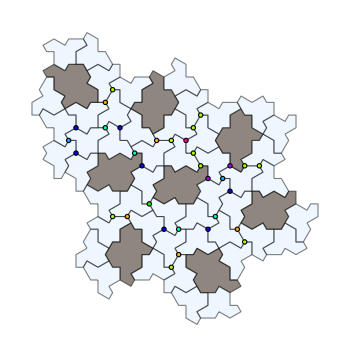
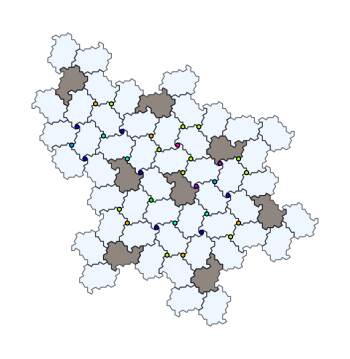
-Graphics-↔^(Combinitorial Equivalent)-Graphics-

```mathematica
Row[{
#1,
Style["↔^(Combinitorial Equivalent)",Red,20],
#2
}]&@@
Function[{tile1,tile2},
With[{codesAndCoordinates=Reap[buildClusterCodes[tile1,tile2][g]]},
Show[{
depictTile[
locateTile[If[TrueQ[#4],tile2,tile1]][#1,#2,#3],
False,
If[TrueQ[#4],ColorNegate[LightBlue],LightBlue]
]&@@@First[codesAndCoordinates]
,
Graphics[
{
EdgeForm[Black],
KeyValueMap[
{#2,Disk[codesAndCoordinates[[2,1,1]][#1],-Subtract@@MinMax[N[tile1["polygonVertices"]]]/30]}&,
Select[Sort[#[[All,1]]]/.color&/@g["vertex"],Head[#]=!=List&]
]
}
]
}
,ImageSize->350
]
]
]@@@{{h1Tile,h2Tile},{h8Tile,h7Tile}}
```

We can see if we only use H1 and H8, what would happen. Maybe helpful to study how H7 form, and why.

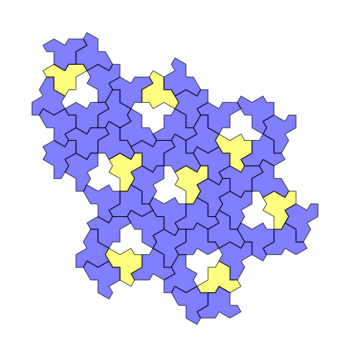
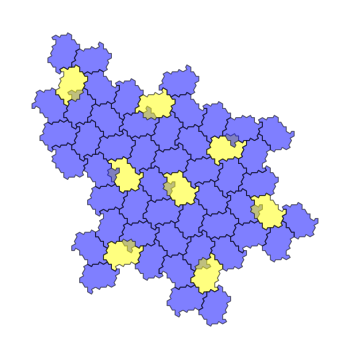
-Graphics-↔^(Combinitorial Equivalent)-Graphics-

```mathematica
Row[{
#1,
Style["↔^(Combinitorial Equivalent)",Red,20],
#2
}]&@@
Function[{tile1,tile2},Show[
depictTile[
locateTile[If[TrueQ[#4],tile2,tile1]][#1,#2,#3],
False,
If[TrueQ[#4],ColorNegate[Blue],Blue]
]&@@@buildClusterCodes[tile1,tile2][g]
,ImageSize->350
]
]@@@{{h1Tile,h1Tile},{h8Tile,h8Tile}}
```

## Other tiling in Hat Family

### Tiles Information

```mathematica
s1Tile=<|
"polygonVertices"->,
"vertices"->
|>;
s2Tile=<|
"polygonVertices"->,
"vertices"->
|>;
```

```mathematica
t1Tile=<|
"polygonVertices"->,
"vertices"->
|>;
t2Tile=<|
"polygonVertices"->,
"vertices"->
|>;
```

### Example

Here we use turtle - Tile (√3, 1), hat - Tile(1,√3) and spectre - Tile(1,1) to construct combinatorial equivalent clusters:

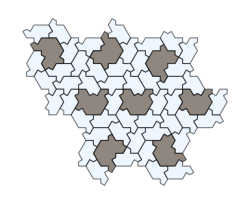
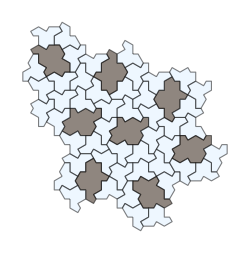
↔^(Comb Equ)-Graphics-Turtle-Tile(√3,1)-Graphics-Hat-Tile(1,√3)-Graphics-Spectre-Tile(1,1)

```mathematica
Row[{
##
},Style["↔^(Comb Equ)",Red,20]]&@@
Function[{tile1,tile2,label},
Labeled[
Show[
depictTile[
locateTile[If[TrueQ[#4],tile2,tile1]][#1,#2,#3],
False,
If[TrueQ[#4],ColorNegate[LightBlue],LightBlue]
]&@@@buildClusterCodes[tile1,tile2][g]
,ImageSize->250
],
Style[label,Italic,Purple,Bold]
]
]@@@{
{t1Tile,t2Tile,"Turtle-Tile(√3,1)"},
{h1Tile,h2Tile,"Hat-Tile(1,√3)"},
{s1Tile,s2Tile,"Spectre-Tile(1,1)"}
}
```

### Dynamic

```mathematica
bigCluster=;
```

```mathematica
g=tilingTopologicalGraph[<|False->h1Tile,True->h2Tile|>][codePreprocess[bigCluster]];
```

```mathematica
formalTile1=formatTile[v1/@Range[14],p/@Range[5]];
formalTile2=formatTile[v2/@Range[20],p/@Range[5]];
```

## Super {6,6,6} Dead End

```mathematica
g=tilingTopologicalGraph[<|False->h1Tile,True->h2Tile|>][codePreprocess[testdata2]];
```

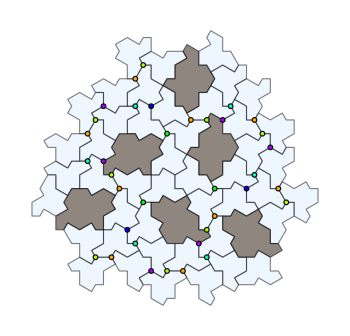
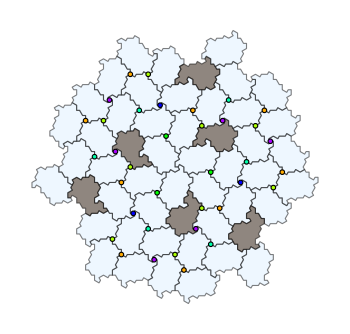
-Graphics-↔^(Combinitorial Equivalent)-Graphics-

```mathematica
Row[{
#1,
Style["↔^(Combinitorial Equivalent)",Red,20],
#2
}]&@@
Function[{tile1,tile2},
With[{codesAndCoordinates=Reap[buildClusterCodes[tile1,tile2][g]]},
Show[{
depictTile[
locateTile[If[TrueQ[#4],tile2,tile1]][#1,#2,#3],
False,
If[TrueQ[#4],ColorNegate[LightBlue],LightBlue]
]&@@@First[codesAndCoordinates]
,
Graphics[
{
EdgeForm[Black],
KeyValueMap[
{#2,Disk[codesAndCoordinates[[2,1,1]][#1],-Subtract@@MinMax[N[tile1["polygonVertices"]]]/30]}&,
Select[Sort[#[[All,1]]]/.color&/@g["vertex"],Head[#]=!=List&]
]
}
]
}
,ImageSize->350
]
]
]@@@{{h1Tile,h2Tile},{h8Tile,h7Tile}}
```

## Super-tiles

```mathematica
h8supertile=formatTile[,{{-5,-11 √3},{0,0},{-14,8 √3},{-31,-5 √3},{-24,-14 √3}}];
h7supertile=formatTile[,{{-5,-11 √3},{0,0},{-14,8 √3},{-31,-5 √3},{-24,-14 √3}}];
```

```mathematica
g=tilingTopologicalGraph[<|False->h1Tile,True->h2Tile|>][codePreprocess[testdata1]];
```

```mathematica
Export[NotebookDirectory[]<>"combinatorialEquivalenceExample.png",
Grid[{Riffle[{##},Style["↔",Red,100]]}]&@@
Function[{tile1,tile2},
With[{codesAndCoordinates=Reap[buildClusterCodes[tile1,tile2][g]]},
(*Show[#,ImageSize->2000]&@*)
Show[{
depictTile[
locateTile[If[TrueQ[#4],tile2,tile1]][#1,#2,#3],
False,
If[TrueQ[#4],Lighter@Green,Blue]
]&@@@First[codesAndCoordinates]
,
Graphics[
{
EdgeForm[Black],
KeyValueMap[
{#2,Disk[codesAndCoordinates[[2,1,1]][#1],-Subtract@@MinMax[N[tile1["polygonVertices"]]]/30]}&,
Select[Sort[#[[All,1]]]/.color&/@g["vertex"],Head[#]=!=List&]
]
}
]
}
,ImageSize->1000
]
]
]@@@{{h1Tile,h2Tile},{h8Tile,h7Tile},{h8supertile,h7supertile}}
]
```

C:\Users\hp\Desktop\Wolfram Summer School\project\Tile\GeneralTile\TopolygicalGraph\combinatorialEquivalenceExample.png